{{-28.7789+0.370484 x},{-17.7728+0.36456 x},{25.5232+0.36319 x},{14.9283+0.360543 x},{-6.00225+0.361658 x},{22.2712+0.358014 x},{33.1311+0.360356 x},{-39.0643+0.367324 x},{15.8375+0.357964 x},{48.1719+0.363662 x},{-21.1051+0.368194 x},{-29.1731+0.367435 x},{-9.92845+0.373402 x},{-18.2625+0.357743 x},{-13.3843+0.358862 x},{1.22788+0.371727 x},{-9.16775+0.37283 x},{6.9643+0.366499 x},{31.0038+0.358157 x}}

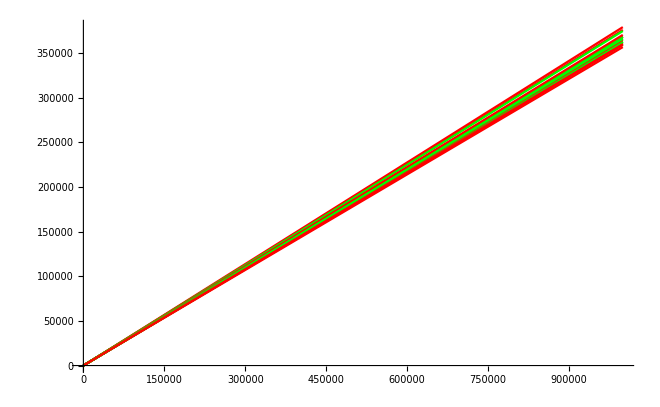

```mathematica
data = ReadList["D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalus\\D_L500OT50000_u10t1.txt", {Number, Number}];
pos=Position[data,{_, 1.0}];
fitf={};
f={};

For[i=1,i<Length@pos,i++,{
refined=Take[data, {pos[[i,1]],pos[[i+1,1]]}], fitrefined=Take[data, {Floor[(pos[[i,1]]+pos[[i+1,1]])/2],pos[[i+1,1]]}],
AppendTo[f,LinearModelFit[refined, {1,x},x]["BestFitParameters"].({{1}, {x}})], AppendTo[fitf,LinearModelFit[fitrefined, {1,x},x]["BestFitParameters"].({{1}, {x}})]}
]
f
Plot[fitf,{x,0,10^6},PlotStyle->{Red,Green}]
```

```mathematica
z={}
For[i=1,i<5,i++,{ Print@i, AppendTo[z,i]}]
z
```

{}

1

2

3

4

{1,2,3,4}